```mathematica
NS["alz_explore"]
```

```mathematica
(* definition of empirical covariance matrix, used a lot in the following *)covmatrix[data_]:=Block[{means=Mean@T@data,numindividuals=Length[data[[1]]]},
((data-means).T[data-means])/numindividuals]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data_alzheimer_RGS"]
```

C:\Users\pglpm\repositories\nanunana\data_alzheimer_RGS

```mathematica
<<"reference_prior.m";
```

```mathematica
fileselect="reduced"; (* "reduced" *)
categories={"healthy","alzheimer","mci"};
categoryfiles={fileselect<>"_RGS_graphprop22_Con.txt",fileselect<>"_RGS_graphprop22_AD.txt",fileselect<>"_RGS_graphprop22_MCI.txt"};
numcategories=Length[categories];
origquantities=Flatten@Import[fileselect<>"_RGS_graphprop22_quantities.txt","CSV"];
orignumquantities=Length@origquantities;

Do[tempdata=Import[categoryfiles[[ii]],"CSV"];
(* transform 2nd moments to raw ones *)
Do[tempdata[[jj]]=Sqrt[tempdata[[jj]]+tempdata[[jj-6]]^2],{jj,7,12}];
(* transform 3nd moments to raw ones *)
Do[tempdata[[jj]]=CubeRoot[tempdata[[jj]]+3*tempdata[[jj-6]]*tempdata[[jj-12]]-2*tempdata[[jj-12]]^3],{jj,13,18}];
(* transform 4nd moments to raw ones *)
Do[tempdata[[jj]]=tempdata[[jj]]+4*tempdata[[jj-6]]*tempdata[[jj-18]]-6*tempdata[[jj-12]]*tempdata[[jj-18]]^2+3*tempdata[[jj-18]]^4,{jj,19,24}];

origsubjectfile[ii]=N@tempdata;
numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
origquantities
```

{graphweights1, shortest path1, cluster coeff.1, weighted degree1, normalized weighted degree1, closeness centrality1, graphweights2, shortest path2, cluster coeff.2, weighted degree2, normalized weighted degree2, closeness centrality2, graphweights3, shortest path3, cluster coeff.3, weighted degree3, normalized weighted degree3, closeness centrality3, graphweights4, shortest path4, cluster coeff.4, weighted degree4, normalized weighted degree4, closeness centrality4}

```mathematica
origsubjectfile[1]//MF
```

(0.110717 | 0.300156 | 0.151385 | 0.147756 | 0.197291 | 0.129257 | 0.25917 | 0.185153 | 0.137658 | 0.150906 | 0.205832 | 0.147286 | 0.410499 | 0.188969 | 0.155966 | 0.246819 | 0.105789 | 0.071421 | 0.154324 | 0.109265 | 0.217588 | 0.336159 | 0.131122 | 0.113975 | 0.123078 | 0.162896
8.01777 | 2.98725 | 5.18893 | 5.97314 | 4.6099 | 6.899 | 3.34505 | 4.46551 | 6.60185 | 5.14802 | 4.08735 | 5.49852 | 2.23757 | 4.57323 | 5.23568 | 3.20899 | 8.52377 | 11.4263 | 4.42359 | 8.09923 | 3.54527 | 2.62722 | 5.89276 | 7.33438 | 6.01905 | 5.12483
0.12001 | 0.323652 | 0.15781 | 0.154955 | 0.203958 | 0.133204 | 0.261508 | 0.154755 | 0.14763 | 0.177105 | 0.193062 | 0.152379 | 0.407154 | 0.195962 | 0.152495 | 0.177294 | 0.110322 | 0.081788 | 0.182355 | 0.122044 | 0.23318 | 0.347783 | 0.113588 | 0.119419 | 0.149602 | 0.151888
0.112802 | 0.308263 | 0.153641 | 0.150175 | 0.200749 | 0.13189 | 0.263036 | 0.187141 | 0.140203 | 0.152863 | 0.208996 | 0.148674 | 0.415327 | 0.1913 | 0.157508 | 0.252424 | 0.107465 | 0.075378 | 0.156659 | 0.110313 | 0.21926 | 0.340021 | 0.132418 | 0.116621 | 0.125441 | 0.165654
0.365564 | 0.553002 | 0.403041 | 0.41436 | 0.4913 | 0.458141 | 0.456899 | 0.433994 | 0.461743 | 0.37142 | 0.445537 | 0.384587 | 0.509542 | 0.396508 | 0.307982 | 0.523646 | 0.446947 | 0.532565 | 0.368309 | 0.42206 | 0.291388 | 0.47734 | 0.328487 | 0.444975 | 0.380686 | 0.433667
0.126138 | 0.339367 | 0.195972 | 0.169618 | 0.219073 | 0.147368 | 0.302438 | 0.227322 | 0.154084 | 0.197861 | 0.247099 | 0.185186 | 0.449743 | 0.221899 | 0.196636 | 0.312411 | 0.118374 | 0.089032 | 0.228601 | 0.126733 | 0.289568 | 0.38596 | 0.172681 | 0.14 | 0.168664 | 0.197566
0.13285 | 0.337147 | 0.182148 | 0.171153 | 0.220838 | 0.148527 | 0.296304 | 0.223975 | 0.15765 | 0.183856 | 0.243361 | 0.176736 | 0.454337 | 0.218679 | 0.188327 | 0.309268 | 0.121519 | 0.085615 | 0.191554 | 0.125839 | 0.276555 | 0.384675 | 0.167999 | 0.140201 | 0.147373 | 0.193867
8.43181 | 3.12878 | 5.42089 | 6.25747 | 4.80392 | 7.26285 | 3.48265 | 4.67013 | 6.95234 | 5.35166 | 4.25989 | 5.7068 | 2.31859 | 4.77062 | 5.49103 | 3.38259 | 8.91886 | 12.2831 | 4.54274 | 8.42982 | 3.72055 | 2.72893 | 6.21127 | 7.83841 | 6.22738 | 5.36517
0.120085 | 0.323952 | 0.159292 | 0.155069 | 0.204059 | 0.133247 | 0.261802 | 0.155945 | 0.147753 | 0.178173 | 0.193828 | 0.153778 | 0.407326 | 0.196132 | 0.152867 | 0.179157 | 0.110457 | 0.0821102 | 0.183932 | 0.122599 | 0.236002 | 0.349394 | 0.114192 | 0.119697 | 0.150604 | 0.152409
0.849391 | 1.81677 | 2.44375 | 1.33885 | 1.39088 | 0.961408 | 2.49491 | 2.07102 | 1.32262 | 3.48797 | 1.76308 | 3.78031 | 3.12918 | 2.49231 | 2.96833 | 1.1752 | 0.939971 | 0.269499 | 3.35428 | 2.87002 | 8.49066 | 5.40141 | 2.51161 | 1.17923 | 2.01864 | 1.14739
0.369171 | 0.559774 | 0.414199 | 0.418707 | 0.494841 | 0.463088 | 0.461404 | 0.437031 | 0.468658 | 0.387355 | 0.449221 | 0.39548 | 0.511505 | 0.401574 | 0.313283 | 0.526435 | 0.451178 | 0.542162 | 0.387165 | 0.435047 | 0.304033 | 0.485201 | 0.334213 | 0.456995 | 0.398431 | 0.436583
0.126932 | 0.341747 | 0.19749 | 0.170759 | 0.220113 | 0.14849 | 0.304146 | 0.228854 | 0.155303 | 0.199721 | 0.248308 | 0.186996 | 0.451131 | 0.223477 | 0.199559 | 0.312789 | 0.118882 | 0.0898556 | 0.230139 | 0.128561 | 0.293397 | 0.388734 | 0.174028 | 0.141502 | 0.170173 | 0.198724
0.34863 | 0.6291 | 0.424087 | 0.411884 | 0.487107 | 0.37655 | 0.581213 | 0.48234 | 0.391512 | 0.425855 | 0.511226 | 0.416368 | 0.74885 | 0.481008 | 0.434599 | 0.584237 | 0.331016 | 0.260327 | 0.434745 | 0.33839 | 0.549782 | 0.679183 | 0.396851 | 0.356241 | 0.371272 | 0.442299
-9.42071 | -2.9554 | -5.80323 | -6.816 | -5.07759 | -7.98182 | -3.42706 | -4.87552 | -7.60048 | -5.76877 | -4.40361 | -6.21411 | -1.90644 | -5.01954 | -5.85993 | -3.24697 | -10.0605 | -13.7895 | -4.85164 | -9.52108 | -3.6758 | -2.46557 | -6.68256 | -8.51527 | -6.89707 | -5.73072
0.34136 | 0.627208 | 0.407251 | 0.40134 | 0.476057 | 0.364732 | 0.553554 | 0.402055 | 0.389307 | 0.437169 | 0.460844 | 0.398351 | 0.713049 | 0.46455 | 0.397573 | 0.43822 | 0.323554 | 0.267086 | 0.445614 | 0.345522 | 0.518865 | 0.6545 | 0.330137 | 0.340496 | 0.393413 | 0.396724
0.822138 | 1.61369 | 2.12312 | 1.18907 | 1.28799 | 0.71351 | 2.26963 | -1.01226 | -0.919774 | 3.69817 | 1.40683 | 3.53872 | 1.453 | 1.84828 | 2.8245 | 1.16383 | 0.522769 | 0.404327 | 4.18865 | 2.59257 | 9.67486 | 5.13074 | -1.68439 | -0.933995 | 2.53944 | 0.787684
0.674763 | 0.839068 | 0.718153 | 0.723234 | 0.789592 | 0.762976 | 0.761657 | 0.74016 | 0.767445 | 0.691514 | 0.751029 | 0.700097 | 0.802756 | 0.706796 | 0.613742 | 0.814274 | 0.752641 | 0.826447 | 0.691821 | 0.737605 | 0.601159 | 0.781795 | 0.636921 | 0.756528 | 0.703248 | 0.739786
0.353096 | 0.646181 | 0.465782 | 0.42568 | 0.498171 | 0.389837 | 0.604258 | 0.509889 | 0.400977 | 0.468865 | 0.535891 | 0.450125 | 0.752871 | 0.502544 | 0.468045 | 0.614614 | 0.33883 | 0.282688 | 0.511709 | 0.355208 | 0.590941 | 0.694633 | 0.43062 | 0.377822 | 0.424567 | 0.467778
0.145729 | 0.598697 | 0.233582 | 0.222639 | 0.337636 | 0.18071 | 0.497666 | 0.315123 | 0.198821 | 0.233821 | 0.365049 | 0.223924 | 0.858821 | 0.32103 | 0.246064 | 0.476406 | 0.13232 | 0.071839 | 0.2431 | 0.139349 | 0.410049 | 0.693302 | 0.19202 | 0.152073 | 0.170234 | 0.259703
8998.09 | 39.0788 | 1202.62 | 2357.89 | 661.619 | 4596.12 | 99.3925 | 558.073 | 3759.02 | 1154.95 | 345.798 | 1589.03 | -11.0073 | 634.087 | 1251.95 | 70.8044 | 11766.2 | 42174.8 | 537.434 | 9373.25 | 146.134 | 4.98547 | 2215.29 | 6062.46 | 2453.82 | 1128.92
0.154111 | 0.641301 | 0.235132 | 0.228148 | 0.342642 | 0.181094 | 0.485643 | 0.228192 | 0.211997 | 0.279119 | 0.316706 | 0.222996 | 0.838581 | 0.32337 | 0.222805 | 0.279952 | 0.135159 | 0.0842163 | 0.29166 | 0.158384 | 0.415837 | 0.700827 | 0.141658 | 0.153015 | 0.216701 | 0.221531
2.19308 | 54.4042 | 110.515 | 8.50065 | 11.3198 | 2.35681 | 128.913 | 41.1217 | 9.12256 | 565.325 | 21.4631 | 515.935 | 276.918 | 135.054 | 280.373 | 5.18021 | 1.92337 | 0.127394 | 1011.82 | 170.109 | 20867.9 | 1867.81 | 145.323 | 6.06429 | 103.691 | 4.3532
0.74427 | 1.10977 | 0.8335 | 0.85585 | 1.00987 | 0.947226 | 0.94487 | 0.897453 | 0.954431 | 0.7644 | 0.921647 | 0.791839 | 1.04157 | 0.816402 | 0.604822 | 1.06505 | 0.924541 | 1.0796 | 0.760928 | 0.875777 | 0.567651 | 0.985277 | 0.655487 | 0.92165 | 0.788616 | 0.896764
0.166798 | 0.680824 | 0.32404 | 0.261819 | 0.380071 | 0.211864 | 0.589187 | 0.400692 | 0.226705 | 0.328767 | 0.44989 | 0.29848 | 0.929638 | 0.387308 | 0.32633 | 0.613456 | 0.151029 | 0.0965881 | 0.40395 | 0.168452 | 0.55797 | 0.791538 | 0.268972 | 0.196093 | 0.25982 | 0.327699)

```mathematica
(*find maxima*)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
maxima=Max/@T[totaldata];allmeans=Mean[totaldata];
```

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;
totaldata=T@totaldata/tempmeans;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=origsubjectfile[ii]/tempmeans,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
(*referencemeans=referencemeans/tempmeans;*)
(*referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];*)
```

```mathematica
Do[data6[ii]=Apply[Times,origsubjectfile[ii]],{ii,numcategories}];
```

```mathematica
data6[1]
```

{244626.,7168.34,9.68854×10^6,711859.,4.73341×10^7,5.82341×10^7,8.94495×10^6,54685.7,1.24251×10^8,1.06785×10^8,1.7335×10^8,1.87828×10^6,6.7696×10^7,833195.,2.95036×10^8,9.93747×10^6,9.73563×10^7,9.92125×10^7,1.97566×10^6,41956.1,5.59753×10^7,2.19786×10^7,448411.,130368.,5.02969×10^6,2.41739×10^6,6.04454×10^7,2.15144×10^6,636.674,4.59457×10^8,293130.,6.49423×10^7,9.91553×10^6,7.91221×10^7,1.70163×10^8,2.4978×10^6,1.25975×10^7,1.67117×10^6,597077.,7.17694×10^6,3.61096×10^7,960153.,4.48767×10^6,1.95236×10^7,1.64894×10^7,2.17698×10^7,1.25463×10^8,7.27029×10^6,183703.,1.86465×10^6,72282.7,1.87009×10^8,2.14974×10^6,3.26406×10^7,1.16934×10^6,8.49728×10^7}

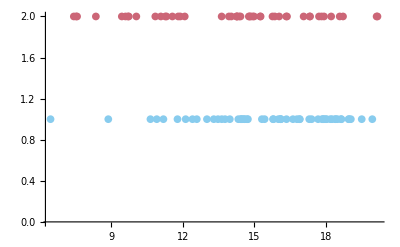

```mathematica
ListPlot[{T@{Log@data6[1],Table[1,numindividuals[1]]},T@{Log@data6[2],Table[2,numindividuals[2]]}}]
```

```mathematica
origsubjectfile[1][[{1,2},;;]]//MF
```

(0.758029 | 0.675088 | 0.852063 | 0.784907 | 0.894786 | 0.903643 | 0.850916 | 0.719425 | 0.917907 | 0.919075 | 0.928697 | 0.808815 | 0.902458 | 0.793282 | 0.944692 | 0.852909 | 0.910941 | 0.9132 | 0.81253 | 0.718038 | 0.896684 | 0.872877 | 0.775716 | 0.743499 | 0.831074 | 0.810508 | 0.899627 | 0.80872 | 0.610898 | 0.95524 | 0.77252 | 0.903004 | 0.848974 | 0.906702 | 0.929063 | 0.820205 | 0.857517 | 0.80165 | 0.779202 | 0.838595 | 0.886659 | 0.799495 | 0.829226 | 0.870926 | 0.864641 | 0.874784 | 0.916878 | 0.843664 | 0.753461 | 0.806436 | 0.730412 | 0.929843 | 0.813457 | 0.882339 | 0.80294 | 0.910465
1.20385 | 1.34973 | 1.04667 | 1.14498 | 0.996083 | 0.987291 | 1.04945 | 1.25684 | 0.969021 | 0.968529 | 0.958027 | 1.10646 | 0.986808 | 1.12969 | 0.941749 | 1.04593 | 0.976813 | 0.974626 | 1.10104 | 1.25342 | 0.992691 | 1.02036 | 1.15724 | 1.2078 | 1.0749 | 1.10333 | 0.99296 | 1.10339 | 1.51264 | 0.930879 | 1.17434 | 0.986587 | 1.05064 | 0.981259 | 0.957721 | 1.09134 | 1.04035 | 1.11743 | 1.14994 | 1.06239 | 1.00459 | 1.12517 | 1.07832 | 1.02366 | 1.03073 | 1.02195 | 0.970134 | 1.05997 | 1.19871 | 1.10993 | 1.24147 | 0.956663 | 1.10186 | 1.00933 | 1.12199 | 0.978566)

```mathematica
Do[plot=ListPlot[Table[T@origsubjectfile[ii][[{aa,bb},;;]],{ii,numcategories}],PlotRange->Auto(*{{0,All},{0,All}}*),PlotMarkers->{{○,20},{△,20},{□,20}},Frame->True,FrameLabel->origquantities[[{aa,bb}]]];
expng["expldata-"<>ToString[aa]<>"_"<>ToString[bb],plot];
,{aa,4,23,6},{bb,aa+6,24,6}]
```

```mathematica
gamma[s_,a_,b_]=Assuming[s>0,FS@PDF[GammaDistribution[a,b],s]]
```

(b^-a ⅇ^(-s/b) s^(-1+a))/Gamma[a]

```mathematica
test1=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[1][[1]],a,b]]]
```

Log[(21620.9 0.0000462515^a b^(-56 a) ⅇ^(-47.0393/b))/Gamma[a]^56]

```mathematica
Integrate[Exp[test1]/(a*b),{a,0,+Infinity},{b,0,+Infinity}]
```

$Aborted

```mathematica
Plot3D[test1-Log[(a*b)],{a,100,500},{b,0.00,0.01},AxesLabel->Auto,PlotPoints->70,PlotRange->{-50,All}]
```

-Graphics3D-

```mathematica
test1=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[1][[2]],a,b]]]
```

Log[(0.0230316 43.4187^a b^(-56 a) ⅇ^(-60.1882/b))/Gamma[a]^56]

```mathematica
max1=NMaximize[{test1,a>0&&b>0},{a,b}]
```

{46.8821,{a→104.595,b→0.0102757}}

```mathematica
test2=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[2][[2]],a,b]]]
```

Log[(0.00270307 369.95^a b^(-48 a) ⅇ^(-54.6605/b))/Gamma[a]^48]

```mathematica
max2=NMaximize[{test2,a>0&&b>0},{a,b}]
```

{29.2594,{a→74.2839,b→0.0153299}}

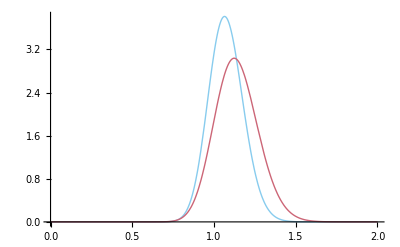

```mathematica
Plot[{gamma[s,a,b]/.max1[[2]],gamma[s,a,b]/.max2[[2]]},{s,0,2},PlotRange->All]
```

```mathematica
ClearAll[test,max];Do[Do[test=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[jj][[ii]],a,b]]];
max[jj]=NMaximize[{test,a>0&&b>0},{a,b}];,{jj,numcategories}];

plot=Plot[Evaluate@Table[gamma[s,a,b]/.max[jj][[2]],{jj,numcategories}],{s,0,2*maxima[[ii]]},PlotRange->All];
expng["mldistr-"<>ToString[ii],plot];,{ii,24}]
```

```mathematica
(Array[a,{3,4}]/Array[b,3])//MF
```

(a[1,1]/b[1] | a[1,2]/b[1] | a[1,3]/b[1] | a[1,4]/b[1]
a[2,1]/b[2] | a[2,2]/b[2] | a[2,3]/b[2] | a[2,4]/b[2]
a[3,1]/b[3] | a[3,2]/b[3] | a[3,3]/b[3] | a[3,4]/b[3])

```mathematica
(origsubjectfile[1]/allmeans)//MF
```

(0.688236 | 1.86582 | 0.941035 | 0.918476 | 1.22639 | 0.803484 | 1.61104 | 1.15094 | 0.855706 | 0.938057 | 1.27949 | 0.915555 | 2.55173 | 1.17466 | 0.969511 | 1.53427 | 0.657602 | 0.443965 | 0.959304 | 0.67921 | 1.35256 | 2.08962 | 0.815077 | 0.708488 | 0.765074 | 1.01259
1.29462 | 0.482348 | 0.837852 | 0.964477 | 0.744357 | 1.11397 | 0.540122 | 0.721042 | 1.06599 | 0.831246 | 0.65998 | 0.887841 | 0.361298 | 0.738436 | 0.8454 | 0.518152 | 1.37633 | 1.84499 | 0.714273 | 1.30777 | 0.572451 | 0.424215 | 0.951498 | 1.18428 | 0.97189 | 0.827501
0.724633 | 1.95424 | 0.952873 | 0.935634 | 1.23152 | 0.804299 | 1.57901 | 0.934427 | 0.891405 | 1.06938 | 1.16573 | 0.92008 | 2.45844 | 1.18324 | 0.920781 | 1.07052 | 0.666136 | 0.493844 | 1.10108 | 0.736914 | 1.40796 | 2.09995 | 0.685856 | 0.721064 | 0.903312 | 0.917115
0.0216341 | 0.0591212 | 0.0294665 | 0.0288018 | 0.0385013 | 0.025295 | 0.0504472 | 0.0358914 | 0.0268893 | 0.0293173 | 0.040083 | 0.0285139 | 0.0796548 | 0.0366891 | 0.0302082 | 0.048412 | 0.0206105 | 0.0144566 | 0.0300454 | 0.0211567 | 0.0420515 | 0.065212 | 0.0253962 | 0.0223665 | 0.0240581 | 0.0317705
0.870853 | 1.31737 | 0.960131 | 0.987096 | 1.17038 | 1.09139 | 1.08843 | 1.03387 | 1.09997 | 0.884803 | 1.06137 | 0.91617 | 1.21384 | 0.944568 | 0.73368 | 1.24744 | 1.06473 | 1.26869 | 0.877392 | 1.00544 | 0.69415 | 1.13713 | 0.782528 | 1.06003 | 0.906877 | 1.03309
0.652813 | 1.75635 | 1.01423 | 0.877838 | 1.13379 | 0.762686 | 1.56523 | 1.17648 | 0.797444 | 1.02401 | 1.27883 | 0.958409 | 2.32759 | 1.14841 | 1.01767 | 1.61685 | 0.612631 | 0.460775 | 1.1831 | 0.655892 | 1.49863 | 1.99749 | 0.89369 | 0.724554 | 0.872901 | 1.02248
0.408469 | 2.6307 | 0.767855 | 0.677955 | 1.1287 | 0.510554 | 2.03193 | 1.161 | 0.575201 | 0.782324 | 1.37067 | 0.722909 | 4.77736 | 1.10674 | 0.820835 | 2.21362 | 0.341759 | 0.169642 | 0.849214 | 0.366489 | 1.7701 | 3.42468 | 0.653197 | 0.454918 | 0.502655 | 0.869845
1.45858 | 0.200835 | 0.602878 | 0.803314 | 0.473456 | 1.08219 | 0.248833 | 0.447452 | 0.99163 | 0.587578 | 0.372294 | 0.668149 | 0.11029 | 0.466915 | 0.61858 | 0.23474 | 1.63195 | 3.09531 | 0.423374 | 1.45789 | 0.28399 | 0.152782 | 0.791495 | 1.2605 | 0.795608 | 0.590548
0.432245 | 3.14567 | 0.760568 | 0.720782 | 1.24813 | 0.532187 | 2.05446 | 0.728948 | 0.654375 | 0.951558 | 1.12612 | 0.708827 | 4.97319 | 1.15305 | 0.700456 | 0.9621 | 0.36571 | 0.202091 | 1.01407 | 0.450535 | 1.66949 | 3.65917 | 0.390863 | 0.429453 | 0.679869 | 0.696265
0.00827257 | 0.0378463 | 0.0684759 | 0.0205537 | 0.0221823 | 0.0105984 | 0.0713733 | 0.0491806 | 0.0200585 | 0.139498 | 0.0356426 | 0.163862 | 0.112276 | 0.0712242 | 0.10103 | 0.0158362 | 0.010131 | 0.000832798 | 0.12901 | 0.0944488 | 0.826624 | 0.334533 | 0.0723318 | 0.0159448 | 0.0467241 | 0.0150955
0.732599 | 1.68437 | 0.922209 | 0.942394 | 1.31627 | 1.15276 | 1.14439 | 1.02668 | 1.18066 | 0.806547 | 1.08476 | 0.84074 | 1.40641 | 0.86685 | 0.527575 | 1.48971 | 1.09423 | 1.58005 | 0.805758 | 1.01738 | 0.496881 | 1.26548 | 0.600426 | 1.12263 | 0.853333 | 1.02458
0.354417 | 2.5691 | 0.857952 | 0.641414 | 1.06577 | 0.48503 | 2.03487 | 1.1521 | 0.530556 | 0.877444 | 1.3563 | 0.769198 | 4.4769 | 1.0986 | 0.876024 | 2.15217 | 0.310887 | 0.177608 | 1.16507 | 0.363571 | 1.89358 | 3.32412 | 0.666205 | 0.440451 | 0.637024 | 0.868708
0.253715 | 2.94769 | 0.53201 | 0.431811 | 0.848016 | 0.268627 | 2.11292 | 0.967702 | 0.319213 | 0.574118 | 1.22908 | 0.487283 | 7.07766 | 0.890898 | 0.652165 | 2.54639 | 0.147591 | 0.0536386 | 0.646539 | 0.166069 | 2.19661 | 4.60565 | 0.464165 | 0.246512 | 0.295214 | 0.626854
1.44969 | 0.0731694 | 0.383649 | 0.589363 | 0.2631 | 0.935044 | 0.10047 | 0.24563 | 0.821947 | 0.362204 | 0.183347 | 0.438733 | 0.0293608 | 0.259885 | 0.402 | 0.0936426 | 1.70149 | 4.59772 | 0.214644 | 1.42277 | 0.125253 | 0.0479469 | 0.591383 | 1.21382 | 0.560978 | 0.371215
0.209529 | 4.11711 | 0.50038 | 0.45134 | 1.02767 | 0.285985 | 2.17421 | 0.468799 | 0.390524 | 0.694551 | 0.890014 | 0.44981 | 8.17206 | 0.91353 | 0.434554 | 0.716862 | 0.163362 | 0.067614 | 0.769465 | 0.225327 | 1.63748 | 5.21686 | 0.182674 | 0.208572 | 0.419991 | 0.432033
0.000241472 | 0.00262695 | 0.00527642 | 0.000888606 | 0.00116122 | 0.000164264 | 0.00689658 | 0.0000980448 | -0.000282111 | 0.0257104 | 0.00170967 | 0.0230924 | 0.00535774 | 0.00398138 | 0.01192 | 0.00081638 | 0.0000587538 | 0.00001017 | 0.0363812 | 0.00904906 | 0.446482 | 0.0750782 | -0.00154136 | -0.000349118 | 0.00808205 | 0.000269916
0.598155 | 2.09973 | 0.88883 | 0.874305 | 1.42944 | 1.18221 | 1.16837 | 0.9829 | 1.23573 | 0.764704 | 1.0724 | 0.776903 | 1.56237 | 0.776019 | 0.374088 | 1.71135 | 1.08886 | 1.93793 | 0.795901 | 1.03998 | 0.372643 | 1.38678 | 0.45131 | 1.17417 | 0.854902 | 0.979445
0.160712 | 3.14072 | 0.606466 | 0.391272 | 0.832666 | 0.257557 | 2.20289 | 0.940353 | 0.29493 | 0.631345 | 1.19611 | 0.519026 | 7.13485 | 0.877533 | 0.639455 | 2.36492 | 0.130998 | 0.0575037 | 0.961162 | 0.171151 | 2.02279 | 4.62306 | 0.414819 | 0.224302 | 0.391031 | 0.614549
0.21184 | 2.8042 | 0.323666 | 0.250464 | 0.554579 | 0.123952 | 1.90913 | 0.685045 | 0.154868 | 0.375466 | 0.956941 | 0.288311 | 8.8779 | 0.646883 | 0.499853 | 2.39927 | 0.0558345 | 0.0146008 | 0.433721 | 0.0662081 | 2.52213 | 5.32424 | 0.291863 | 0.114504 | 0.159897 | 0.391775
1.2932 | 0.0238131 | 0.221142 | 0.38812 | 0.130439 | 0.733098 | 0.0363653 | 0.121582 | 0.619243 | 0.198902 | 0.0803683 | 0.256594 | 0.00697138 | 0.130112 | 0.23636 | 0.0332303 | 1.58924 | 6.12581 | 0.0956185 | 1.23786 | 0.0499881 | 0.0133639 | 0.404643 | 1.06836 | 0.349118 | 0.209633
0.084902 | 4.50653 | 0.278284 | 0.236297 | 0.707056 | 0.128381 | 1.9249 | 0.255665 | 0.194882 | 0.427171 | 0.591925 | 0.241104 | 11.22 | 0.605251 | 0.226128 | 0.455838 | 0.0610773 | 0.0190139 | 0.493766 | 0.0947188 | 1.36079 | 6.2525 | 0.0719993 | 0.0849695 | 0.218643 | 0.225389
0.0000306298 | 0.000867658 | 0.00171613 | 0.000131506 | 0.000180129 | 0.0000321896 | 0.00208407 | 0.000617156 | 0.000137365 | 0.00883674 | 0.000340985 | 0.00804055 | 0.00425347 | 0.00206794 | 0.00435983 | 0.0000842618 | 0.0000260728 | 2.77678×10^-7 | 0.015684 | 0.00262852 | 0.321753 | 0.030599 | 0.00213913 | 0.0000911154 | 0.00164541 | 0.0000621022
0.475837 | 2.5636 | 0.860508 | 0.79089 | 1.50465 | 1.17983 | 1.16304 | 0.909578 | 1.26096 | 0.754788 | 1.02883 | 0.723278 | 1.66985 | 0.679871 | 0.262753 | 1.89823 | 1.05135 | 2.34637 | 0.861944 | 1.07296 | 0.293383 | 1.50152 | 0.33239 | 1.20665 | 0.921877 | 0.905191
0.0626503 | 3.30097 | 0.367919 | 0.204768 | 0.555437 | 0.117184 | 2.04028 | 0.656474 | 0.14057 | 0.392365 | 0.901125 | 0.302817 | 9.68062 | 0.60123 | 0.406286 | 2.20442 | 0.0470805 | 0.0160884 | 0.6863 | 0.0703882 | 1.87658 | 5.52221 | 0.221433 | 0.0979956 | 0.20822 | 0.371702)

```mathematica
(origsubjectfile[2]/allmeans)//MF
```

(0.579241 | 0.737791 | 1.93991 | 0.74594 | 0.545512 | 0.500023 | 0.712323 | 0.39096 | 0.859386 | 0.726807 | 1.09372 | 0.589131 | 0.978947 | 1.18629
1.46995 | 1.19099 | 0.409357 | 1.20303 | 1.62694 | 1.69383 | 1.25573 | 2.14301 | 1.04108 | 1.19861 | 0.820258 | 1.39898 | 0.822361 | 0.680882
0.589965 | 0.794602 | 2.36596 | 0.734088 | 0.563403 | 0.491296 | 0.731142 | 0.408025 | 0.86052 | 0.763723 | 1.06383 | 0.624249 | 1.05119 | 1.15663
0.732688 | 1.34299 | 2.63346 | 2.20936 | 0.807837 | 0.694192 | 1.09883 | 0.458333 | 1.40524 | 1.03148 | 1.6872 | 1.0542 | 2.26524 | 3.66002
0.954352 | 1.02376 | 1.04816 | 1.0043 | 1.19899 | 0.773275 | 1.01177 | 0.92724 | 1.0965 | 1.06867 | 1.30797 | 0.870581 | 0.975297 | 0.708226
0.580202 | 0.711429 | 2.10139 | 0.705203 | 0.519189 | 0.502602 | 0.67722 | 0.395819 | 0.811526 | 0.707646 | 1.02341 | 0.607435 | 1.0314 | 1.27074
0.294938 | 0.437007 | 3.37255 | 0.427903 | 0.23011 | 0.235246 | 0.404643 | 0.133865 | 0.57806 | 0.423228 | 0.889468 | 0.318815 | 0.796284 | 1.38321
1.92261 | 1.21855 | 0.144137 | 1.23353 | 2.27503 | 2.55431 | 1.36498 | 4.06389 | 0.936553 | 1.2399 | 0.573724 | 1.70877 | 0.573185 | 0.413168
0.286795 | 0.520993 | 4.73672 | 0.443577 | 0.261698 | 0.199161 | 0.440256 | 0.137185 | 0.60978 | 0.480954 | 0.931411 | 0.325566 | 0.9184 | 1.11431
0.172495 | 0.58719 | 2.4222 | 1.54917 | 0.208757 | 0.154346 | 0.385495 | 0.067281 | 0.625729 | 0.342794 | 0.892596 | 0.369746 | 1.69886 | 4.43746
0.889248 | 1.03679 | 1.16595 | 0.972667 | 1.3973 | 0.581931 | 0.993085 | 0.836724 | 1.15764 | 1.11807 | 1.62999 | 0.766207 | 0.956911 | 0.504869
0.281403 | 0.421372 | 3.75446 | 0.414143 | 0.223704 | 0.211075 | 0.383459 | 0.130687 | 0.546494 | 0.417565 | 0.863906 | 0.308079 | 0.886317 | 1.36627
0.132025 | 0.218271 | 4.90998 | 0.204786 | 0.0789514 | 0.10692 | 0.196986 | 0.0413961 | 0.321201 | 0.207985 | 0.569013 | 0.153992 | 0.543678 | 1.47493
2.25712 | 1.09267 | 0.0440965 | 1.11315 | 2.782 | 3.43807 | 1.30473 | 6.86389 | 0.742549 | 1.1255 | 0.350574 | 1.84643 | 0.349347 | 0.228435
0.113408 | 0.2782 | 7.86241 | 0.217799 | 0.0989241 | 0.0657652 | 0.21553 | 0.0375205 | 0.351256 | 0.246521 | 0.662522 | 0.139545 | 0.657365 | 0.881822
0.0286144 | 0.183173 | 1.71105 | 0.760082 | 0.0380253 | 0.0241911 | 0.0951612 | 0.00699603 | 0.194499 | 0.0809622 | 0.326536 | 0.0948744 | 0.928705 | 3.91315
0.808212 | 1.03706 | 1.37891 | 0.912492 | 1.58898 | 0.427357 | 0.949471 | 0.740383 | 1.18106 | 1.15083 | 1.94446 | 0.682942 | 0.947371 | 0.362379
0.114148 | 0.208284 | 5.74641 | 0.202893 | 0.0801956 | 0.0741776 | 0.182091 | 0.0361152 | 0.306097 | 0.206087 | 0.603134 | 0.130781 | 0.636303 | 1.24076
0.053421 | 0.0965432 | 6.12561 | 0.0869176 | 0.0232772 | 0.0475595 | 0.0886617 | 0.0120847 | 0.156271 | 0.0925464 | 0.306974 | 0.0669269 | 0.326808 | 1.44461
2.42017 | 0.875947 | 0.0119153 | 0.905029 | 3.03304 | 4.18666 | 1.11783 | 10.5075 | 0.52931 | 0.915372 | 0.191485 | 1.79389 | 0.190934 | 0.116689
0.0375226 | 0.124418 | 11.0649 | 0.0893816 | 0.0312989 | 0.0181963 | 0.088237 | 0.00858659 | 0.169178 | 0.105775 | 0.393808 | 0.0504174 | 0.395959 | 0.588963
0.00371284 | 0.0451837 | 1.01581 | 0.290923 | 0.00543769 | 0.00297418 | 0.0184158 | 0.000576286 | 0.0470197 | 0.0151503 | 0.0921138 | 0.0197146 | 0.411468 | 2.78242
0.715897 | 1.02202 | 1.70765 | 0.83207 | 1.76752 | 0.306741 | 0.8867 | 0.646648 | 1.16764 | 1.16936 | 2.22863 | 0.614221 | 0.947142 | 0.261314
0.0397183 | 0.0882424 | 7.76328 | 0.0851289 | 0.0245737 | 0.0223848 | 0.0745147 | 0.00858836 | 0.146475 | 0.0874309 | 0.357813 | 0.0477235 | 0.392263 | 0.974213)

```mathematica
(origsubjectfile[3]/allmeans)//MF
```

(0.974627 | 0.535871 | 0.567132 | 0.657919 | 0.820068 | 1.11885 | 0.620349 | 0.550255 | 2.4143 | 1.02683 | 0.872489 | 0.745804 | 1.32971 | 1.22537 | 1.13835 | 0.908176
0.939211 | 1.4724 | 1.53698 | 1.39043 | 0.994748 | 0.761415 | 1.35962 | 1.51954 | 0.361833 | 0.866067 | 0.967974 | 1.0465 | 0.672685 | 0.701564 | 0.742184 | 0.929529
0.950096 | 0.543158 | 0.633699 | 0.667422 | 0.802029 | 1.11474 | 0.624732 | 0.533237 | 2.24137 | 1.0215 | 0.949148 | 0.725291 | 1.29183 | 1.17243 | 1.06646 | 0.934783
2.34544 | 0.595163 | 0.822355 | 1.0149 | 1.34095 | 1.72597 | 1.07179 | 0.645088 | 6.55499 | 1.71074 | 1.69586 | 1.51865 | 2.62561 | 6.76731 | 2.03703 | 1.54107
1.1931 | 0.905774 | 0.754579 | 1.20072 | 0.953104 | 0.903611 | 0.952685 | 0.922295 | 1.02512 | 1.07509 | 1.06995 | 0.694266 | 1.05444 | 0.91262 | 1.01717 | 0.945004
0.894337 | 0.578675 | 0.552048 | 0.605546 | 0.852334 | 1.123 | 0.620316 | 0.564308 | 2.34914 | 0.976435 | 0.87597 | 0.810279 | 1.25237 | 1.20826 | 1.1524 | 0.908601
0.704694 | 0.267078 | 0.300661 | 0.321947 | 0.599858 | 1.05947 | 0.316808 | 0.276823 | 4.81025 | 0.818044 | 0.605138 | 0.534202 | 1.37611 | 1.18516 | 1.13186 | 0.677263
0.746906 | 1.90985 | 2.0634 | 1.65558 | 0.860791 | 0.507111 | 1.58854 | 2.07423 | 0.112573 | 0.644686 | 0.791546 | 0.950617 | 0.386753 | 0.41357 | 0.48136 | 0.739
0.74255 | 0.244587 | 0.336848 | 0.366454 | 0.533602 | 1.02832 | 0.321715 | 0.235268 | 4.15441 | 0.858826 | 0.74547 | 0.437178 | 1.37318 | 1.1338 | 0.949001 | 0.721781
1.72862 | 0.114383 | 0.219034 | 0.325177 | 0.579993 | 0.959458 | 0.365836 | 0.133996 | 13.6668 | 0.927274 | 0.942278 | 0.745635 | 2.17257 | 14.61 | 1.33813 | 0.763184
1.35916 | 0.805001 | 0.560364 | 1.38299 | 0.890319 | 0.799083 | 0.878288 | 0.832261 | 1.01564 | 1.11275 | 1.13971 | 0.473512 | 1.06469 | 0.807358 | 1.0138 | 0.872012
0.660206 | 0.280518 | 0.254237 | 0.303393 | 0.60518 | 1.05861 | 0.318784 | 0.267833 | 4.60371 | 0.792196 | 0.6405 | 0.546751 | 1.29815 | 1.21581 | 1.11484 | 0.685271
0.40932 | 0.118863 | 0.170453 | 0.127168 | 0.38191 | 0.887256 | 0.140952 | 0.122755 | 8.09225 | 0.542915 | 0.348176 | 0.371148 | 1.18175 | 0.966473 | 0.95128 | 0.43907
0.517371 | 2.19368 | 2.43576 | 1.72252 | 0.657994 | 0.300475 | 1.62771 | 2.55535 | 0.0308828 | 0.421499 | 0.560055 | 0.762716 | 0.194607 | 0.212482 | 0.277437 | 0.512437
0.471278 | 0.0901233 | 0.148737 | 0.163403 | 0.290628 | 0.774457 | 0.134812 | 0.0847627 | 6.28486 | 0.586678 | 0.478097 | 0.215963 | 1.18569 | 0.892704 | 0.694564 | 0.45435
0.882749 | 0.0156405 | 0.0416978 | 0.0724861 | 0.178442 | 0.378045 | 0.0875404 | 0.0196771 | 19.9711 | 0.351335 | 0.37934 | 0.261523 | 1.24885 | 22.1698 | 0.624819 | 0.267713
1.48513 | 0.704651 | 0.411739 | 1.53418 | 0.81894 | 0.693365 | 0.785785 | 0.734995 | 0.976305 | 1.11449 | 1.21765 | 0.319365 | 1.03384 | 0.694957 | 0.994285 | 0.789005
0.40339 | 0.11424 | 0.0979832 | 0.126111 | 0.358889 | 0.838906 | 0.136042 | 0.107011 | 7.53706 | 0.535422 | 0.392707 | 0.307852 | 1.1166 | 1.02147 | 0.906415 | 0.430252
0.203571 | 0.0482577 | 0.111213 | 0.0435315 | 0.215013 | 0.689656 | 0.0574541 | 0.0492361 | 11.9184 | 0.318943 | 0.174308 | 0.253095 | 0.899056 | 0.698356 | 0.694647 | 0.259864
0.318892 | 2.2715 | 2.57 | 1.59881 | 0.452475 | 0.161544 | 1.49383 | 2.88207 | 0.00761314 | 0.247399 | 0.350282 | 0.55051 | 0.0875401 | 0.0974185 | 0.14444 | 0.316708
0.249843 | 0.0279427 | 0.056273 | 0.0608652 | 0.133238 | 0.48952 | 0.0472825 | 0.0256434 | 7.98015 | 0.334939 | 0.257429 | 0.08984 | 0.855438 | 0.588562 | 0.429425 | 0.239778
0.348269 | 0.00169364 | 0.00632192 | 0.0125273 | 0.0435154 | 0.117524 | 0.0163502 | 0.00226877 | 22.7865 | 0.103791 | 0.123427 | 0.0731738 | 0.555912 | 26.3445 | 0.230864 | 0.074112
1.56209 | 0.608617 | 0.300205 | 1.64403 | 0.743942 | 0.591436 | 0.683713 | 0.635009 | 0.913013 | 1.08439 | 1.31006 | 0.2141 | 0.968627 | 0.583678 | 0.961438 | 0.70198
0.20962 | 0.040148 | 0.0324802 | 0.0446837 | 0.182629 | 0.573455 | 0.0495199 | 0.0369176 | 10.5777 | 0.309712 | 0.20782 | 0.148504 | 0.818806 | 0.736143 | 0.635264 | 0.231102)

```mathematica
gamma[s,a,b]^3
```

(b^(-3 a) ⅇ^(-(3 s)/b) s^(-3+3 a))/Gamma[a]^3

```mathematica
Integrate[gamma[ss,a,b]^4,{a,0,100},{b,0,Infinity},Assumptions->n>1]
```

NIntegrate[gamma[ss,a,b]^4,{a,0,100},{b,0,∞},Assumptions→n>1]

```mathematica
Series[(n^(-n a) Gamma[n a])/(a ss^n Gamma[a]^n),{a,0,0}]
```

Gamma[a]^-n (ss^-n/(n a^2)-(ss^-n (EulerGamma+Log[n]))/a+1/12 n ss^-n (6 EulerGamma^2+π^2+12 EulerGamma Log[n]+6 Log[n]^2)+O[a]^1)

```mathematica
Series[(n^(-n a) Gamma[n a])/(a ss^n Gamma[a]^n),{a,+Infinity,0}]
```

2^(-Floor[1/2+Arg[a n]/(2 π)]) ⅇ^((-n+n Log[a]-n Log[n]+n Log[(-1)^Floor[1/2+Arg[n]/(2 π)] n]) a+1/2 (-Log[a]-Log[(-1)^Floor[1/2+Arg[n]/(2 π)] n]+Log[2 π])+1/(12 n a)+O[1/a]^2) Csc[a n π]^Floor[1/2+Arg[a n]/(2 π)] Gamma[a]^-n (ss^-n/a+O[1/a]^2)

```mathematica
Limit[(n^(-n a) Gamma[n a])/(a ss^n Gamma[a]^n),a->0,Assumptions->(n>1&&0<ss<1)]
```

Limit[(n^(-a n) ss^-n Gamma[a]^-n Gamma[a n])/a,a→0,Assumptions→n>1&&0<ss<1]

```mathematica
Assuming[n>1,FS@Series[gamma[ss,a,b]^n/(a*b),{a,0,1},{b,0,1}]]
```

((a ⅇ^(-ss/b))/ss)^n ((1/b+O[b]^2)/a+((n (EulerGamma-Log[b]+Log[ss]))/b+O[b]^2)+(1/(12 b)n (6 EulerGamma^2 n-π^2+6 n (Log[b]-Log[ss]) (-2 EulerGamma+Log[b]-Log[ss]))+O[b]^2) a+O[a]^2)

```mathematica
(* improper prior *)
{referencenumber ,referencemeans,referencecovariance}= {0,Table[0,{orignumquantities}],Table[0,{orignumquantities},{orignumquantities}]};
```

```mathematica
fileh=origsubjectfile[1];filea=origsubjectfile[2];
```

```mathematica
minnumindividuals
```

48

```mathematica
orignumquantities
```

24

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;
totaldata=T@totaldata/tempmeans;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=origsubjectfile[ii]/tempmeans,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
referencemeans=referencemeans/tempmeans;
(*referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];*)
```

```mathematica
fileh=origsubjectfile[1];filea=origsubjectfile[3];
```

```mathematica
(* Pareto II distribution, obtained as gamma mixture of exponentials*)par[x_,a_,b_]=PDF[ParetoDistribution[b,a,0],x];
```

```mathematica
(* means and number of samples, for pareto distr *)Do[omeans[ii]=Mean@T[origsubjectfile[ii]];onind[ii]=numindividuals[ii],{ii,numcategories}];
```

```mathematica
(* product of Paretos for the quantities *)ClearAll[prob];
prob[x_,cat_]:=Product[par[x[[ii]],onind[cat],onind[cat]*omeans[cat][[ii]]],{ii,orignumquantities}];
```

```mathematica
Do[
success[cati]=Table[
(*success=0;
avdistr=Table[0,{ii,numcategories}];*)
datum=T[origsubjectfile[cati]][[ii]];
(*Print[datum];
Print[prob[datum,1]];
Print[par[datum[[1]],onind[1],onind[1]*omeans[1][[1]]]];
Print[par[datum[[1]],onind[2],onind[2]*omeans[2][[1]]]];*)
distr=Normalize[Table[prob[datum,jj],{jj,numcategories}],Total]

(*If[Last@Ordering[distr,-1]==cati,++success,Null];
avdistr=avdistr+distr;*)
,{ii,numindividuals[cati]}];
,{cati,2}]
```

```mathematica
success[1]//MF
```

(0.359168 | 0.640832
0.207514 | 0.792486
0.585994 | 0.414006
0.436239 | 0.563761
0.672638 | 0.327362
0.687288 | 0.312712
0.581026 | 0.418974
0.298661 | 0.701339
0.72003 | 0.27997
0.718822 | 0.281178
0.738953 | 0.261047
0.492138 | 0.507862
0.689253 | 0.310747
0.454646 | 0.545354
0.766485 | 0.233515
0.58625 | 0.41375
0.706895 | 0.293105
0.710105 | 0.289895
0.498625 | 0.501375
0.30295 | 0.69705
0.678799 | 0.321201
0.62986 | 0.37014
0.41794 | 0.58206
0.353934 | 0.646066
0.542491 | 0.457509
0.498736 | 0.501264
0.681761 | 0.318239
0.497147 | 0.502853
0.0807556 | 0.919244
0.785185 | 0.214815
0.393291 | 0.606709
0.689022 | 0.310978
0.58124 | 0.41876
0.698014 | 0.301986
0.739114 | 0.260886
0.513411 | 0.486589
0.59711 | 0.40289
0.478592 | 0.521408
0.428477 | 0.571523
0.56207 | 0.43793
0.657179 | 0.342821
0.461711 | 0.538289
0.536502 | 0.463498
0.624175 | 0.375825
0.61274 | 0.38726
0.630131 | 0.369869
0.718775 | 0.281225
0.564819 | 0.435181
0.364238 | 0.635762
0.488236 | 0.511764
0.314266 | 0.685734
0.741438 | 0.258562
0.499333 | 0.500667
0.649468 | 0.350532
0.46896 | 0.53104
0.703152 | 0.296848)

```mathematica
success[2]//MF
```

(0.487098 | 0.512902
0.796201 | 0.203799
0.307786 | 0.692214
0.520412 | 0.479588
0.308004 | 0.691996
0.193296 | 0.806704
0.44818 | 0.55182
0.599311 | 0.400689
0.596046 | 0.403954
0.251474 | 0.748526
0.528335 | 0.471665
0.470695 | 0.529305
0.524226 | 0.475774
0.64986 | 0.35014
0.534673 | 0.465327
0.128635 | 0.871365
0.463731 | 0.536269
0.169864 | 0.830136
0.484905 | 0.515095
0.699169 | 0.300831
0.479881 | 0.520119
0.725322 | 0.274678
0.453497 | 0.546503
0.30029 | 0.69971
0.638617 | 0.361383
0.359968 | 0.640032
0.5644 | 0.4356
0.237093 | 0.762907
0.274857 | 0.725143
0.792037 | 0.207963
0.652214 | 0.347786
0.312578 | 0.687422
0.515835 | 0.484165
0.225526 | 0.774474
0.505115 | 0.494885
0.135236 | 0.864764
0.512818 | 0.487182
0.338841 | 0.661159
0.480119 | 0.519881
0.310366 | 0.689634
0.684023 | 0.315977
0.670276 | 0.329724
0.679709 | 0.320291
0.235531 | 0.764469
0.583726 | 0.416274
0.71724 | 0.28276
0.565494 | 0.434506
0.348523 | 0.651477)

```mathematica
Mean@success[1]
```

{0.555281,0.444719}

```mathematica
Mean@success[2]
```

{0.467938,0.532062}

```mathematica
Det[covmatrix[totaldata]]
```

1.26769×10^-34

```mathematica
rdata=Table[RandomInteger[{-100,100},4],{3}];
```

```mathematica
Det[covmatrix[rdata]]//N
```

1.95436×10^9

```mathematica
(* model comparison by studying P(M|D) ∝ P(D|M). The latter is given by a matrix t-distribution *)
```

```mathematica
subjectfile[1]=filea;subjectfile[2]=filem;subjectfile[3]=fileh;
ClearAll[nindividuals,uu,cc,pp];
Do[nindividuals[ii]=Length[subjectfile[ii][[1]]];uu[ii]=Table[{1},{nindividuals[ii]}];
cc[ii]=IdentityMatrix[nindividuals[ii]]-uu[ii].T[uu[ii]]/(z+nindividuals[ii]);
,{ii,numcategories}];

pp={1,1,1}/3;
```

```mathematica
numquantities=3;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
Length@setofquantities
```

3276

```mathematica
AbsoluteTiming[testcv=ParallelTable[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];crossvalidateall[{filea[[quant]],filem[[quant]],fileh[[quant]]},pp,0]
,{ll, Length@setofquantities},Method->"CoarsestGrained"];]
```

$Aborted

```mathematica
score[data_]:=data[[1,1]]^2*data[[2,1]]*data[[3,1]]^2;ClearAttributes[score,Listable];
```

```mathematica
bestcv=Ordering[score/@testcv[[1;;10]],-2]
```

{7,6}

```mathematica
testcv[[1;;10]]//N
```

{{{0.428571,0.421798},{0.,0.279573},{0.653846,0.342766}},{{0.214286,0.28012},{0.8125,0.473374},{0.307692,0.402347}},{{0.785714,0.550458},{0.,0.289014},{1.,0.999497}},{{0.5,0.323067},{0.1875,0.28157},{0.230769,0.311644}},{{0.714286,0.381832},{0.,0.227961},{0.269231,0.32131}},{{0.5,0.37511},{0.3125,0.352646},{0.269231,0.342054}},{{0.5,0.33938},{0.125,0.255084},{0.423077,0.36248}},{{0.5,0.316384},{0.125,0.277673},{0.269231,0.377671}},{{0.285714,0.362208},{0.625,0.318173},{0.192308,0.325054}},{{0.,0.130455},{0.75,0.485839},{0.346154,0.372663}}}

```mathematica
Listable
```

```mathematica
testcv==testcvp
```

False

```mathematica
Max[testcv-testcvp]
```

0.535392

```mathematica
ClearAll[quant,means,s0];
testresp=ParallelTable[
quant=setofquantities[[ll]];
Exp@Sum[
(* this is for N<d *)
(* 
means[ii]=Mean@T[subjectfile[ii][[quant]]];s0[ii]=T[{means[ii]}].{means[ii]}+IdentityMatrix[numquantities]*nindividuals[ii];

(*nindividuals[ii]*Log[pp[[ii]]]*)
-(nindividuals[ii]/2)*Log[(Pi*Det[s0[ii]]*Exp@Total@Log@Select[Eigenvalues[Inverse[s0[ii]].(covmatrix[subjectfile[ii][[quant]]]*nindividuals[ii])],#>0&])] *)
(* this is for N>d *)
Log[
Product[Gamma[(nindividuals[ii]+1-jj)/2],{jj,numquantities}]/nindividuals[ii]^(numquantities/2)/Det[Pi*covmatrix[subjectfile[ii][[quant]]]*nindividuals[ii]]^(nindividuals[ii]/2)]

,{ii,numcategories}]
,{ll,Length@setofquantities}
,Method->"CoarsestGrained"
];
```

```mathematica
best=Ordering[testresp,-2]
```

{54,1192}

```mathematica
testresp[[best]]
```

{1.78681×10^45,4.54472×10^46}

```mathematica
setofquantities[[best]]
```

{{1,4,7},{4,17,23}}

```mathematica
<<"results_3_4.m";
```

```mathematica
(({resultsa3[[#]],resultsm3[[#]],resultsh3[[#]]})&/@best)//N
```

{{{64.2857,47.0512},{31.25,39.5835},{100.,99.9251}},{{0.,3.54992},{87.5,83.6004},{92.3077,87.7812}}}

```mathematica
<<"crossvalidate.m";
```

```mathematica
selq=setofquantities[[best[[2]]]]
```

{4,17,23}

```mathematica
rea=crossvalidate1[filea[[selq]],{filem[[selq]],fileh[[selq]]},pp,0];
```

```mathematica
Evaluate@Array[re3,3]=crossvalidateall[{filea[[selq]],filem[[selq]],fileh[[selq]]},pp,0];
```

```mathematica
Array[re3,3]*100//N
```

{{0.,3.54992},{87.5,83.6004},{92.3077,87.7812}}

```mathematica
Abort
```

```mathematica
Return
```

```mathematica
(({resultsa4[[#]],resultsm4[[#]],resultsh4[[#]]})&/@best)//N
```

{{{0.,3.58436},{75.,68.8091},{34.6154,39.9044}},{{0.,8.04221},{81.25,76.6917},{96.1538,96.4751}}}

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa3)*(score/@resultsm3)*(score/@resultsh3);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
AbsoluteTiming[
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


resultsh3=ParallelTable[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits=totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

If[Last@Ordering[distr,-1]==1,++hits,Null];
totpr=totpr+distr[[1]];

,{ndat,aindividuals}];

100*{hits,totpr}/aindividuals

,{ll,Length@setofquantities},Method->"CoarsestGrained"];
]
```

{50.017,Null}

```mathematica
(* some analysis shows that selecting eigenvector seems to be a bad idea *)eigenvectors=T[Eigenvectors[covmatrix[totaldata]]];
ieigenvectors=Inverse[eigenvectors];

Do[origsubjectfile[ii]=ieigenvectors.origsubjectfile[ii],{ii,numcategories}];
totaldata=ieigenvectors.totaldata;

referencemeans=ieigenvectors.referencemeans;
referencecovariance=ieigenvectors.referencecovariance.eigenvectors;
```

```mathematica
(* we can use at most (num.subjects -2) quantities. We choose those that have the covariance matrix with largest volume *)

(* this selects all possible subsets of (num.subjs-2) quantities out of all available quantities *)
(*numusedquantities=minnumindividuals-2;*)
numusedquantities=24;

trialquantities=Subsets[Range[orignumquantities],{numusedquantities}];
totcovmatrix=covmatrix[totaldata];

(* this calculates all determinants of cov. matrices for these subsets *)
trialdeterminants=Table[Abs@Det[totcovmatrix[[ii,ii]]],{ii,trialquantities}];

(* this is the subset with largest scatter *)
bestquantities=Ordering[trialdeterminants,-1][[1]];
chosenquantities=trialquantities[[bestquantities]];
ClearAll[trialquantities,trialdeterminants];
origquantities[[chosenquantities]]
```

{graphweights1, shortest path1, cluster coeff.1, weighted degree1, normalized weighted degree1, closeness centrality1, graphweights2, shortest path2, cluster coeff.2, weighted degree2, normalized weighted degree2, closeness centrality2, graphweights3, shortest path3, cluster coeff.3, weighted degree3, normalized weighted degree3, closeness centrality3, graphweights4, shortest path4, cluster coeff.4, weighted degree4, normalized weighted degree4, closeness centrality4}

```mathematica
relevant={1,2,3,8,9,12,15,16,20,21,23,24}
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
chosenquantities=relevant
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
chosenquantities={1,2,3,7,10,13,14,18,19,21,22};
```

```mathematica
qqq=Sort@RandomSample[relevant,3];Print[qqq];
ListPointPlot3D[Evaluate@Table[origsubjectfile[ii][[qqq]],{ii,3}],BoxRatios->1,PlotStyle->{{PointSize[Large],red},{PointSize[Large],blue},{PointSize[Large],green}},PlotRange->All,ViewPoint->Dynamic[viewpoint],AxesLabel->myaxes[origquantities[[qqq]]]]
```

```mathematica
expng["discrete_quantities"]
```

./discrete_quantities.png

```mathematica
(* select subsets of data, for each category, corresponding to the optimal quantities *)
quantities=origquantities[[chosenquantities]];numquantities=Length@quantities;
Do[subjectfile[ii]=origsubjectfile[ii][[chosenquantities]],{ii,numcategories}];

nreferencemeans=referencemeans[[chosenquantities]];
nreferencecovariance=referencecovariance[[chosenquantities,chosenquantities]];
```

```mathematica
Do[means[ii]=Mean@T@subjectfile[ii];
tparameter[ii]=numindividuals[ii]+1-numquantities;
tcovariance[ii]=covmatrix[ subjectfile[ii]];
,{ii,numcategories}];
```

```mathematica
orde=Ordering[Product[Abs@Diagonal[covmatrix[origsubjectfile[ii]]],{ii,numcategories}],8]
```

{4,21,16,15,22,18,24,9}

```mathematica
numtry=RandomSample[Range[orignumquantities],8];
```

```mathematica
Do[omeans[ii]=Mean[T[origsubjectfile[ii]]];ocovm[ii]=Symmetrize@covmatrix[origsubjectfile[ii]];,{ii,numcategories}]
```

```mathematica
Array[omeans,3]//T//MF
```

(-0.375824 | -0.0672789 | 0.243769
0.547065 | 0.04255 | -0.320758
-0.283451 | -0.100243 | 0.214315
0.360124 | 0.801578 | -0.687192
-0.0148227 | -0.176416 | 0.116545
-0.377064 | -0.0947126 | 0.261319
-0.232532 | -0.0735923 | 0.170497
0.502016 | -0.0303538 | -0.251637
0.208745 | -0.183399 | 0.000459583
-0.151903 | -0.141906 | 0.169121
0.218832 | -0.389348 | 0.121766
0.0642604 | -0.101096 | 0.0276111
-0.0449675 | 0.0932653 | -0.0331808
-0.283438 | 0.0381687 | 0.129132
-0.366819 | 0.170934 | 0.0923281
-0.120383 | -0.188291 | 0.180693
0.0667007 | -0.259964 | 0.124062
0.334983 | -0.211461 | -0.0502454
-0.114415 | 0.0379939 | 0.0382272
0.439699 | -0.0975029 | -0.176759
0.372862 | -0.15382 | -0.106114
-0.138748 | -0.123718 | 0.150845
0.0445739 | -0.345985 | 0.188912
0.311777 | -0.140375 | -0.0814952)

```mathematica
vector=Array[x,2];
```

```mathematica
intb=ReplacePart[Table[{x[ii],-Infinity,+Infinity},{ii,2}],0->Sequence]
```

Sequence[{x[1],-∞,∞},{x[2],-∞,∞}]

```mathematica
NIntegrate[Product[PDF[MultinormalDistribution[omeans[ii],ocovm[ii]],vector],{ii,numcategories}],Evaluate@intb,PrecisionGoal->2,AccuracyGoal->Infinity,MinRecursion->20,MaxRecursion->20]
```

$Aborted

```mathematica
Product[PDF[MultinormalDistribution[omeans[ii][[{2}]],ocovm[ii][[{2},{2}]]],{x}],{ii,numcategories}]
```

0.075244 ⅇ^(-0.3953 (-0.547065+x)^2-0.655943 (-0.04255+x)^2-0.677018 (0.320758+x)^2)

```mathematica
Mod[3,3]+1
```

1

```mathematica
numusedquantities=3;

trialquantities=Subsets[Range[orignumquantities],{numusedquantities}];
```

```mathematica
vector=Array[x,numusedquantities];intb=ReplacePart[Table[{x[ii],-Infinity,+Infinity},{ii,numusedquantities}],0->Sequence] ;overl=Table[inte=NIntegrate[Product[PDF[MultinormalDistribution[omeans[ii][[ll]],ocovm[ii][[ll,ll]]],vector],{ii,numcategories}],Evaluate@intb,PrecisionGoal->1,AccuracyGoal->+Infinity];Print[ll,inte];inte,{ll,trialquantities}];
```

$Aborted

```mathematica
NIntegrate[Product[PDF[MultinormalDistribution[omeans[ii][[{16,18,22}]],ocovm[ii][[{16,18,22},{16,18,22}]]],vector],{ii,numcategories}],Evaluate@intb,PrecisionGoal->1,AccuracyGoal->+Infinity,WorkingPrecision->30]
```

0.256235251781658096449378647753

```mathematica
overl[[1;;10]]
```

{0.0515084,0.,0.00363415,0.172348,0.0253653,0.0335705,0.00624655,0.00640976,0.0028607,0.00820197}

```mathematica
Ordering[overl,9]
```

{2,23,44,45,46,47,48,49,50}

```mathematica
trialquantities[[45]]
```

{1,4,6}

```mathematica
chosenquantities=Union@Flatten@trialquantities[[Ordering[overl,2]]]
```

{1,2,3,4}

```mathematica
mnumind[1]=pnumind[1]-1;
mmean[1]=(pnumind[1]*pmean[1]-datax)/mnumind[1];
mcovmatr[1]=Symmetrize[(pnumind[1]*pcovmatr[1]-(T[{mmean[1]-datax}].{mmean[1]-datax})*mnumind[1]/pnumind[1])/mnumind[1]];
```

```mathematica
numquantities=4;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
```

```mathematica
Length[setofquantities]
```

20475

```mathematica
origsubjectfile[3]=filea;origsubjectfile[2]=filem;origsubjectfile[1]=fileh;
Do[numindividuals[ii]=Length[origsubjectfile[ii][[1]]];,{ii,numcategories}];
```

```mathematica
AbsoluteTiming[
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


resultsh4=ParallelTable[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits=totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

If[Last@Ordering[distr,-1]==1,++hits,Null];
totpr=totpr+distr[[1]];

,{ndat,aindividuals}];

100*{hits,totpr}/aindividuals

,{ll,Length@setofquantities},Method->"CoarsestGrained"];
]
```

{532.729,Null}

```mathematica
Max[resultsa4[[;;,1]]]//N
```

92.8571

```mathematica
Max[resultsm4[[;;,1]]]//N
```

100.

```mathematica
Max[resultsh4[[;;,1]]]//N
```

100.

```mathematica
Save["results_3_4.m",{resultsa3,resultsm3,resultsh3,resultsa4,resultsm4,resultsh4}];
```

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa4)*(score/@resultsm4)*(score/@resultsh4);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
perc
```

64

```mathematica
best3=Ordering[prodscore,-2]
```

{8515,3395}

```mathematica
{resultsa4,resultsm4,resultsh4}[[;;,best,;;]]//N
```

{{{64.2857,48.4086},{64.2857,57.6419}},{{68.75,57.9062},{68.75,56.1796}},{{100.,99.6817},{96.1538,95.5082}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best]]
```

{{ weighted degree1, closeness centrality1, normalized weighted degree4, mean across time},{ shortest path1, weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
{resultsa4,resultsm4,resultsh4}[[;;,best3,;;]]//N
```

{{{64.2857,48.4086},{64.2857,57.6419}},{{68.75,57.9062},{68.75,56.1796}},{{100.,99.6817},{96.1538,95.5082}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best3]]
```

{{ weighted degree1, closeness centrality1, normalized weighted degree4, mean across time},{ shortest path1, weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
(* three *)
```

```mathematica
aindividuals
```

16

```mathematica
numquantities=3;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
```

```mathematica
Length[setofquantities]
```

3276

```mathematica
setofquantities={relevant};numquantities=Length[setofquantities[[1]]]
```

12

```mathematica
setofquantities={RandomSample[Range[orignumquantities],12]};
numquantities=Length[setofquantities[[1]]]
```

12

```mathematica
origsubjectfile[1]=filea;origsubjectfile[2]=filem;origsubjectfile[3]=fileh;
Do[numindividuals[ii]=Length[origsubjectfile[ii][[1]]];,{ii,numcategories}];
```

```mathematica
AbsoluteTiming[
ClearAll[hits];
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


results3[1]=ParallelTable[(* cycle through possible graph properties *)
Block[{hits},quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits[1]=0;hits[2]=0;hits[3]=0;totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

++(hits[Last@Ordering[distr,-1]]);
totpr=totpr+distr;

,{ndat,aindividuals}];

{Array[hits,3],totpr}/aindividuals]

,{ll,Length@setofquantities},Method->"CoarsestGrained"];
]
```

{30.706,Null}

```mathematica
Min[results3[1][[;;,1,1]]]//N
```

0.

```mathematica
results3[1]*100//N
```

{{{7.14286,78.5714,14.2857},{7.95794,75.8653,16.1767}}}

```mathematica
Binomial[28,12]
```

30421755

```mathematica
Max[results3[1][[;;,2,1]]]//N
```

0.833256

```mathematica
Ordering[results3[1][[;;,1,1]],1]
```

{15}

```mathematica
results3[1][[15]]*100//N
```

{{0.,85.7143,14.2857},{8.88721,68.0531,23.0597}}

```mathematica
se
```

```mathematica
Max[resultsm3[[;;,1]]]//N
```

100.

```mathematica
origquantities[[setofquantities[[15]]]]
```

{graphweights1, shortest path1, cluster coeff.3}

```mathematica
chosenquantities={1,2,3,7,10,13,14,18,19,21,22};
```

```mathematica
qqq=setofquantities[[15]];
ListPointPlot3D[Evaluate@Table[origsubjectfile[ii][[qqq]],{ii,3}],BoxRatios->1,PlotStyle->{{PointSize[Large],red},{PointSize[Large],blue},{PointSize[Large],green}},PlotRange->All,ViewPoint->Dynamic[viewpoint],AxesLabel->myaxes[origquantities[[qqq]]]]
```

-Graphics3D-

```mathematica
expng["discrete_quantities"]
```

./discrete_quantities.png

```mathematica
Max[resultsh3[[;;,1]]]//N
```

100.

```mathematica
score[datum_]:=datum[[1,1]];score3[datum_]:=datum[[1,1]]^3;
```

```mathematica
prodscore=(score3/@results3[1])*(score/@results3[2])*(score3/@results3[3]);
```

```mathematica
best=Ordering[prodscore,-2]
```

{1119,1170}

```mathematica
Table[results3[ii][[1200]],{ii,3}]*100//N
```

{{{92.8571,7.14286,0.},{70.3447,29.6553,1.20625×10^-30}},{{31.25,68.75,0.},{46.961,53.039,4.66608×10^-34}},{{96.1538,0.,3.84615},{91.1279,3.25304,5.61911}}}

```mathematica
Table[results3[ii][[1170]],{ii,3}]*100//N
```

{{{85.7143,14.2857,0.},{83.3256,16.6744,6.43593×10^-20}},{{56.25,43.75,0.},{58.4382,41.5618,7.2857×10^-24}},{{92.3077,0.,7.69231},{87.5696,4.13524,8.29517}}}

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa3)*(score/@resultsm3)*(score/@resultsh3);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
perc
```

64

```mathematica
best3=Ordering[prodscore,-2]
```

{3276,1146}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best3,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best3]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
Ordering[resultsa3,-2]
```

{1170,1200}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,%,;;]]//N
```

{{{85.7143,83.3256},{92.8571,70.3447}},{{56.25,58.4382},{31.25,46.961}},{{92.3077,87.5696},{96.1538,91.1279}}}

```mathematica
origquantities[[#]]&/@setofquantities[[%%]]
```

{{ weighted degree1, graphweights3, weighted degree4},{ weighted degree1, weighted degree3, graphweights4}}

```mathematica
ClearAll[score,prodscore];score[number_]:=number[[1]];
score2[number_]:=number[[2]]^2;
```

```mathematica
perc=100;While[(--perc);
prodscore=(score2/@resultsa4)*(score/@resultsm4)*(score2/@resultsh4);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
prodscore=(score2/@resultsa4)*(score/@resultsm4)*(score2/@resultsh4);
```

```mathematica
Ordering[prodscore,-2]
```

{8951,3419}

```mathematica
{resultsa4,resultsm4,resultsh4}[[;;,%,;;]]//N
```

{{{85.7143,78.3422},{92.8571,82.2203}},{{62.5,60.6178},{62.5,57.7674}},{{96.1538,95.3746},{96.1538,95.7878}}}

```mathematica
setofquantities=Subsets[Range[orignumquantities],{4}];origquantities[[#]]&/@setofquantities[[%526]]
```

{{ weighted degree1, shortest path2, graphweights3, weighted degree4},{ shortest path1, weighted degree1, graphweights3, weighted degree4}}

```mathematica
setofquantities[[%526]]
```

{{4,10,15,24},{2,4,15,24}}

```mathematica
setofquantities[[2]]
```

{1}

```mathematica
(* general average test inferring one datum from all the rest *)
ClearAll[sample,prob,distr,distr2];
testminusonedata[dataall_,ind_,numsamples_:10000]:=
(
precision=Auto;
pp={1,1,1}/3;
numcat=Length[dataall];
numquant=Length[dataall[[1]]];
maindata=dataall[[1]];

(* full data for cat. 1 *)
tempnum=(individuals=Length[maindata[[1]]]);
tempmean=Mean@T[maindata];
pnumind[1]=tempnum;
pmean[1]=tempmean;
pcovmatr[1]=Symmetrize[covmatrix[maindata]];

Do[(* data for other categories without the additional datum *)
dmaindata=dataall[[ii]];
tempnum=Length[dmaindata[[1]]];
tempmean=Mean@T[dmaindata];
mnumind[ii]=tempnum;
mmean[ii]=tempmean;
mcovmatr[ii]=Symmetrize[covmatrix[dmaindata]];
,{ii,2,numcat}];

datax=Flatten[T[maindata][[ind]]];

(* find sufficient statistics minus eliminated datum in first cat. *)
mnumind[1]=pnumind[1]-1;
mmean[1]=(pnumind[1]*pmean[1]-datax)/mnumind[1];
mcovmatr[1]=Symmetrize[(pnumind[1]*pcovmatr[1]-(T[{mmean[1]-datax}].{mmean[1]-datax})*mnumind[1]/pnumind[1])/mnumind[1]];

Do[(* find suff. statistics for other categories plus extra datum *)
pnumind[ii]=mnumind[ii]+1;
pmean[ii]=(mnumind[ii]*mmean[ii]+datax)/pnumind[ii];
pcovmatr[ii]=Symmetrize[(
mnumind[ii]*mcovmatr[ii]+
(T[{mmean[ii]-datax}].{mmean[ii]-datax})*
mnumind[ii]/pnumind[ii])/pnumind[ii]];
,{ii,2,numcat}];

(* distribution to sample the Normal-Inv-Wishart prior from *)
distr=Table[pp[[ii]]*PDF[MultivariateTDistribution[mmean[ii],mcovmatr[ii]*(mnumind[ii]+1)/(mnumind[ii]+1-numquant),mnumind[ii]+1-numquant],datax],{ii,numcategories}];distr=distr/Total[distr];

newsample=Table[(* create samples for prior parameters *)
kk=RandomChoice[distr->Range[numcat]];

Do[(* the non-selected is has prob. conditional on data minus the extra datum *)
svar[ii]=RandomVariate[InverseWishartMatrixDistribution[mnumind[ii],mcovmatr[ii]*mnumind[ii]],WorkingPrecision->precision];
smean[ii]=RandomVariate[MultinormalDistribution[mmean[ii],svar[ii]/mnumind[ii]],WorkingPrecision->precision];

,{ii,Drop[Range[numcat],{kk}]}];

(* the selected is has prob. conditional on data plus the extra datum *)
svar[kk]=RandomVariate[InverseWishartMatrixDistribution[pnumind[kk],pcovmatr[kk]*pnumind[kk]],WorkingPrecision->precision];
smean[kk]=RandomVariate[MultinormalDistribution[pmean[kk],svar[kk]/pnumind[kk]],WorkingPrecision->precision];

(* construct probability vector for categories with the parameters just sampled *)
distr2=Table[pp[[ii]]*PDF[MultinormalDistribution[smean[ii],svar[ii]],datax],{ii,numcat}];
distr2=distr2/Total[distr2]

,{numsamples}];

{distr,newsample}

);
```

```mathematica
{proba,sample}=testminusonedata[{filea[[{2,4,15,24},;;]],filem[[{2,4,15,24},;;]],fileh[[{2,4,15,24},;;]]},14,1000];
```

```mathematica
viewpointh={-2.158703721114823,-2.3659285575604585,1.0919616774250367};
```

```mathematica
histbins=Append[Table[ii,{ii,0,1-1/10,1/10}],1001/1000]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1001/1000}

```mathematica
Mean[sample]
```

{0.988933,0.0110666,6.13102295794426×10^-29043}

```mathematica
sample[[1;;10]]
```

{{0.999999,1.41009×10^-6,1.49650813469701×10^-56225},{1.,6.61779×10^-8,1.18365291575311×10^-63905},{0.999784,0.00021564,1.69014342418627×10^-61138},{0.999999,5.27169×10^-7,1.1865356685814×10^-91171},{0.999432,0.000567981,2.33689663547576×10^-53556},{1.,5.77374×10^-19,9.71100208850502×10^-76183},{1.,1.71676×10^-9,3.07868241491358×10^-65952},{0.99998,0.0000195691,6.86827398741379×10^-73022},{1.,3.33504×10^-9,7.24177841156426×10^-149172},{1.,8.15755×10^-8,6.65736940733134×10^-67426}}

```mathematica
proba
```

{0.986547,0.0134533,1.19302×10^-52}

```mathematica
Do[{proba,sample}=testminusonedata[{filea[[{2,4,15,24},;;]],filem[[{2,4,15,24},;;]],fileh[[{2,4,15,24},;;]]},indi,500];
sample=sample[[;;,{1,2,3}]];proba=proba[[{1,2,3}]];
Print[indi,Chop@proba*100,Chop@Mean[sample]*100];
his=Histogram3D[Chop[sample[[;;,{2,1}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],PlotLabel->mylabels[{P[A,M,H]==Chop[proba]*100}],ViewPoint->Dynamic[viewpointh]];
expng["hist_AD_ind"<>ToString[indi],his];,{indi,14}]
```

```mathematica
(* All quantities *)
numquantities=12;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
```

```mathematica
Length[setofquantities]
```

1

```mathematica
origsubjectfile[1]=filea;origsubjectfile[2]=filem;origsubjectfile[3]=fileh;
Do[numindividuals[ii]=Length[origsubjectfile[ii][[1]]];,{ii,numcategories}];
```

```mathematica
AbsoluteTiming[
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


resultsa28=Table[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=Identity[covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii]];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits=totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=Identity[covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1]];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

If[Last@Ordering[distr,-1]==1,++hits,Null];
totpr=totpr+distr[[1]];

,{ndat,aindividuals}];

100*{hits,totpr}/aindividuals

,{ll,Length@setofquantities}(*,Method->"CoarsestGrained"*)];
]
```

{0.759451,Null}

```mathematica
Eigenvalues[tmatrix[1]]
```

{-6.11503×10^12,-187203.,-104244.,-53903.3,-167.544,-10.5588,-1.25913,-0.367869,-0.129944,-0.0548452,-0.00679079,-0.0000205143,4.2817×10^-12,-7.8851×10^-13,-5.28403×10^-16,4.75335×10^-16,8.96519×10^-17,-3.84983×10^-17,-2.79701×10^-17,-1.65281×10^-17,4.9092×10^-18,7.25177×10^-19,-6.41288×10^-19,-4.02156×10^-19,1.27539×10^-19,-1.40879×10^-20,3.35758×10^-21,-1.20967×10^-21}

```mathematica
Max[resultsa3[[;;,1]]]//N
```

92.8571

```mathematica
Max[resultsm3[[;;,1]]]//N
```

100.

```mathematica
Max[resultsh3[[;;,1]]]//N
```

100.

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa3)*(score/@resultsm3)*(score/@resultsh3);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
perc
```

64

```mathematica
best3=Ordering[prodscore,-2]
```

{3276,1146}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best3,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best3]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
Ordering[resultsa3,-2]
```

{1170,1200}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,%,;;]]//N
```

{{{85.7143,83.3256},{92.8571,70.3447}},{{56.25,58.4382},{31.25,46.961}},{{92.3077,87.5696},{96.1538,91.1279}}}

```mathematica
origquantities[[#]]&/@setofquantities[[%%]]
```

{{ weighted degree1, graphweights3, weighted degree4},{ weighted degree1, weighted degree3, graphweights4}}